## Instability on increasing gain for RHP zero sys. (Problem 3.13)

```mathematica
Clear["Global`*"]
```

```mathematica
G0mp= 1/(1+s); G0ap=(1-s/2)/(1+s/2); G0= G0mp G0ap; K0=Kp; KG0=K0 G0;
```

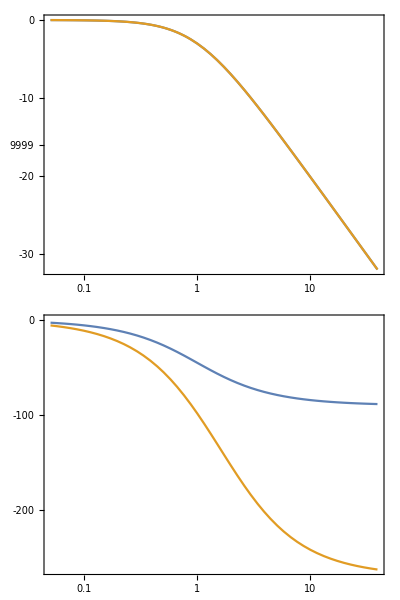

```mathematica
BodePlot[{G0mp,G0}]
```

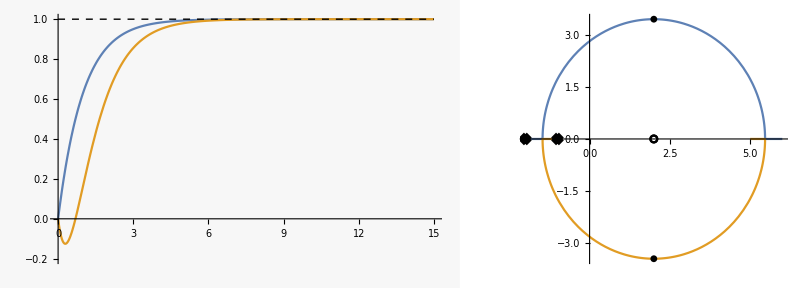

```mathematica
u0 = {1, 0Sin[t]}UnitStep[t];        tmax=15;        trange = {t,0,tmax};
y0=OutputResponse[TransferFunctionModel[G0mp,s],u0,trange];
y1=OutputResponse[TransferFunctionModel[G0,s],u0,trange];

p1=Plot[{y0,y1,1},trange,PlotRange->{-0.2,1},PlotStyle->{,,{Dashed,Thin,Black}}];
p2=RootLocusPlot[KG0,{Kp,0,14}];
GraphicsRow[{p1,p2}]
```

Investigate root locus numerically, then analytically

```mathematica
T0=(K0 G0)/(1+K0 G0)//Simplify
```

-(Kp (-2+s))/(2-Kp (-2+s)+3 s+s^2)

```mathematica
den=Denominator[T0]
```

2-Kp (-2+s)+3 s+s^2

```mathematica
sol=s/.Solve[den==0,s]
```

{1/2 (-3+Kp-√(1-14 Kp+Kp^2)),1/2 (-3+Kp+√(1-14 Kp+Kp^2))}

```mathematica
{1/2 (-3+Kp-√(1-14 Kp+Kp^2)),1/2 (-3+Kp+c)}
```

{1/2 (-3+Kp-√(1-14 Kp+Kp^2)),1/2 (-3+c+Kp)}

```mathematica
Solve[1-14 Kp+Kp^2==0,Kp]
```

{{Kp→7-4 √3},{Kp→7+4 √3}}

```mathematica
{k1=Kp/.Solve[sol[[1]]==sol[[2]],Kp],k1//N}
```

{{7-4 √3,7+4 √3},{0.0717968,13.9282}}

by eye, it is clear that Kp=3 makes Re[s]==0

```mathematica
sol/.Kp->3
```

{-2 ⅈ √2,2 ⅈ √2}

```mathematica
{ssol=sol[[1]]/.Kp->k1//Simplify,ssol//N}
```

{{2-2 √3,2 (1+√3)},{-1.4641,5.4641}}

check that locus is a circle centered on s=2  2Re[s]=Kp-3, 2Im[s]= √(1-14 Kp+Kp^2)

```mathematica
√(1/4((Kp-3-4)^2-(1-14 Kp+Kp^2)))//Simplify  (* radius of circle *)
```

2 √3